```mathematica
solar = Import["/Users/dowoerne/Desktop/solar_data.csv","table",FieldSeparators->";"];
```

```mathematica
η = 0.15;
Subscript[E, sol]= solar[[All,5]];
Subscript[H, total]=400000000; (* GH/s *)
Subscript[H, miner]=;(* GH/s / J*)
Subscript[Consumption, Miner]= 1.9; (* Watt / chip *)
Subscript[Cost, Miner]= 7 ;
Subscript[Reward, BTC] = 150 ;(* BTC / h *)
Subscript[Reward, $]=37500; (* $ / h *)
Subscript[A, sol]=4;
Subscript[n, max]= Ceiling[Ceiling[Subscript[A, sol] * Max[solar[[All,5]]]*η]/Subscript[Consumption, Miner]];
```

```mathematica
Revenue[E_,n_]:= η * E * Subscript[H, miner]/Subscript[H, total]*Subscript[Reward, $] /; n*Subscript[Consumption, Miner] > η*E
```

```mathematica
Revenue[E_,n_]:=n*Subscript[Consumption, Miner]* Subscript[H, miner]/Subscript[H, total]*Subscript[Reward, $] /; n*Subscript[Consumption, Miner] ≤ η*E
```

```mathematica
YearlyRevenue = Total[Table[Revenue[x,y],{x,Subscript[A, sol]*Subscript[E, sol]},{y,Range[1,Subscript[n, max]]}],{1}];
```

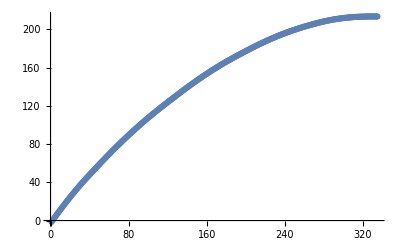

```mathematica
ListPlot[YearlyRevenue]
```

```mathematica
Length[Subscript[E, sol]]
```

8040

```mathematica
n=5
```

5

```mathematica
Rev = 0;
Subscript[E, bat]=0;
```

```mathematica
Subscript[Revenue, bat][A_, n_]:= (
Bat ={1};
Rev=0;
Ebat=0;
Do[
If[n*Subscript[Consumption, Miner] > A* η*Subscript[E, sol][[i]],
If[n*Subscript[Consumption, Miner]-A * η*Subscript[E, sol][[i]] ≥Ebat,ΔE=Ebat;Ebat=0,ΔE=n*Subscript[Consumption, Miner]-A*η*Subscript[E, sol][[i]];Ebat=Ebat-(n*Subscript[Consumption, Miner]-A*η*Subscript[E, sol][[i]])];Rev = Rev + (A*η * Subscript[E, sol][[i]]+ΔE) * Subscript[H, miner]/Subscript[H, total]*Subscript[Reward, $]; ,Rev = Rev +n*Subscript[Consumption, Miner]  * Subscript[H, miner]/Subscript[H, total]*Subscript[Reward, $]; Ebat= A*η*Subscript[E, sol][[i]]-n*Subscript[Consumption, Miner]];
Bat = Append[Bat,Ebat];,{i,Length[Subscript[E, sol]]}];
Return[{Rev,Max[Bat]}]);
```

```mathematica
YearlyReveneueWithBattery = Map[Subscript[Revenue, bat][0.1,#]&,Range[1,20,1]];
```

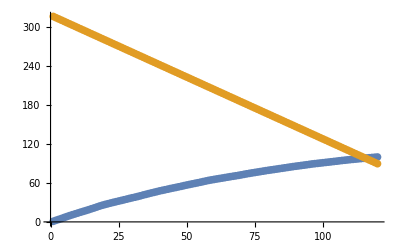

```mathematica
ListPlot[{YearlyReveneueWithBattery[[All,1]],YearlyReveneueWithBattery[[All,2]]}] (* A = 2*)
```

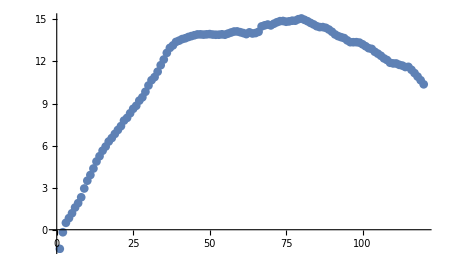
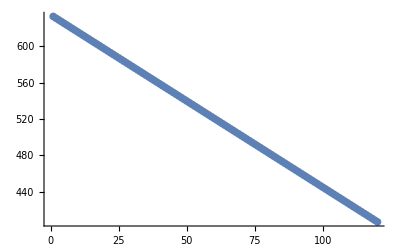

```mathematica
{ListPlot[YearlyReveneueWithBattery[[All,1]]-Range[1,120]],ListPlot[YearlyReveneueWithBattery[[All,2]]]} (* A = 4 *)
```

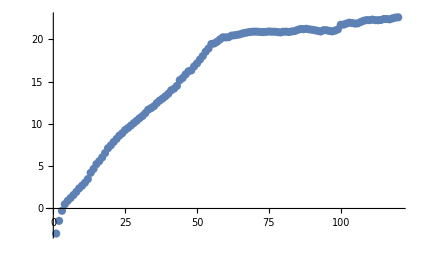
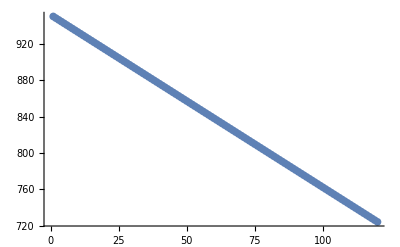

```mathematica
{ListPlot[YearlyReveneueWithBattery[[All,1]]-Range[1,120]],ListPlot[YearlyReveneueWithBattery[[All,2]]]} (* A = 6 *)
```

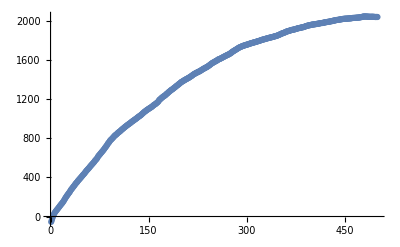
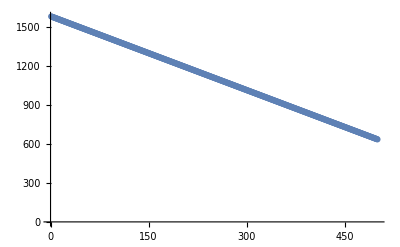

```mathematica
{ListPlot[10*YearlyReveneueWithBattery[[All,1]]-5*Range[1,500]],ListPlot[YearlyReveneueWithBattery[[All,2]]]}
```

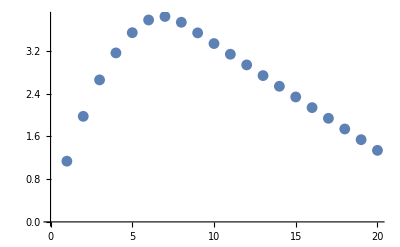
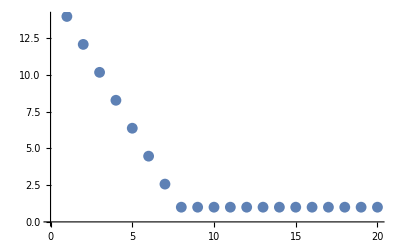

```mathematica
{ListPlot[YearlyReveneueWithBattery[[All,1]]-Range[1,20]/5],ListPlot[YearlyReveneueWithBattery[[All,2]]]}
```